1. NALOGA

```mathematica
trikotnik = {{0, 0}, {5, 1}, {7, 4}}
```

{{0,0},{5,1},{7,4}}

```mathematica
stranice[{AA_, BB_, CC_}] :={{BB, CC}, {CC, AA}, {AA, BB}}
koti[{AA_, BB_, CC_}] := {{CC, AA, BB}, {AA, BB, CC}, {BB, CC, AA}}
SlikaOglisc[trikotnik_] := Map[Point, trikotnik]
SlikaStranic[trikotnik_] := Map[Line, stranice[trikotnik]]
```

```mathematica
stranice[trikotnik]
```

{{{5,1},{7,4}},{{7,4},{0,0}},{{0,0},{5,1}}}

```mathematica
koti[trikotnik]
```

{{{7,4},{0,0},{5,1}},{{0,0},{5,1},{7,4}},{{5,1},{7,4},{0,0}}}

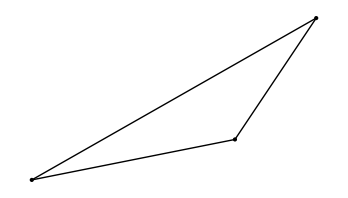

```mathematica
Graphics[{SlikaOglisc[trikotnik],SlikaStranic[trikotnik]}]
```

2. NALOGA

```mathematica
VektorSimetraleKota[{x_, y_, z_}] := Normalize[Normalize[x-y] + Normalize[z-y]]
SimetralaKota[{x_, y_, z_}, dol_: 10] := {y, y + VektorSimetraleKota[{x, y, z}] * dol}
```

```mathematica
alfa = koti[trikotnik][[1]]
VektorSimetraleKota[alfa] // N
SimetralaKota[alfa] // N
```

{{7,4},{0,0},{5,1}}

{0.936505,0.350655}

{{0.,0.},{9.36505,3.50655}}

```mathematica
Graphics[{GrayLevel[0.5],PointSize[0.01],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik], Line[SimetralaKota[alfa]]}]
```

3. NALOGA

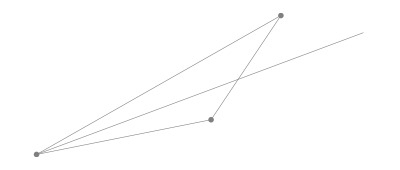

```mathematica
Map[Line, Map[SimetralaKota, koti[trikotnik]]] // N
```

{Line[{{0.,0.},{9.36505,3.50655}}],Line[{{5.,1.},{-0.564397,9.30888}}],Line[{{7.,4.},{-0.310274,-2.82348}}]}

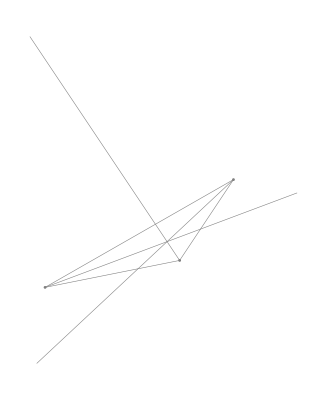

```mathematica
Graphics[{GrayLevel[0.5],PointSize[0.005],Thickness[0.001], SlikaOglisc[trikotnik], SlikaStranic[trikotnik], Map[Line, Map[SimetralaKota, koti[trikotnik]]]}]
```

4. NALOGA

```mathematica
AA = trikotnik[[1]]
BB = trikotnik[[2]]
alfa = koti[trikotnik][[1]]
beta = koti[trikotnik][[2]]
```

{0,0}

{5,1}

{{7,4},{0,0},{5,1}}

{{0,0},{5,1},{7,4}}

```mathematica
AA + r*VektorSimetraleKota[alfa]/.Solve[AA + r*VektorSimetraleKota[alfa] == BB + s*VektorSimetraleKota[beta], {r, s}] //First//N
```

{4.53302,1.6973}

```mathematica
PresecisceSimetral[trikotnik_]:=Module[{AA, BB, alfa, beta},
AA = trikotnik[[1]];
BB = trikotnik[[2]];
alfa = koti[trikotnik][[1]];
beta = koti[trikotnik][[2]];
AA + r*VektorSimetraleKota[alfa]/.Solve[AA + r*VektorSimetraleKota[alfa] == BB + s*VektorSimetraleKota[beta], {r, s}]//First
]
```

```mathematica
PresecisceSimetral[trikotnik] //N
```

{4.53302,1.6973}